```mathematica
Quit
```

For more information about how the geodesics triangles are computed refer to: 2306.12488.

## Numerical Triangles

### Solutions GR

```mathematica
(*Kottler*)
fKot[x_]:=1-1/x-x^2Λb/3/.Λb->1.5*10^(-32)
fUKot[u_]:=(fKot[1/u]);(*Change x->1/u*)
(*Schwarzschild*)
fSch[x_]:=1-1/x
fUSch[u_]:=fSch[1/u]
```

### Setting conditions

```mathematica
RSun=6.957*10^5(*Sun Radii in km*);
rsSun = 2.95 (*Schwarzschild Sun Radii km*);
RSun/rsSun (*Sun Radii in terms o Sch Radii*);
```

```mathematica
b=10 ;(*Impact Parameter*) 
ϵ=1/b; 
ϕmin=0.3; (*Initial angle for the left*)
ϕmax=π-ϕmin;(*Initial angle for the right*)
b2= 1.5 b ;(*b2 and b3 impact parameters, corresponding to adyacent geodesics*)
ϵ1= 1/b2;
δval=10^-8//N; (*Aproaching value to π/2*)
n=4;(*significant digits for initial condition*)
```

### Kottler Triangle

{{u→InterpolatingFunction[…]}}

{{u→InterpolatingFunction[…]}}

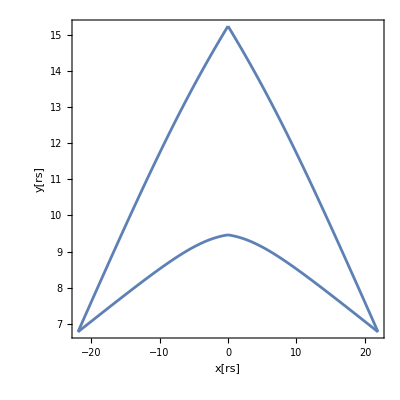

```mathematica
(*Setting the condition u'[π/2]==0*)
(*Note that if you take all the significants digits for the initial condition, the solution for the Differential equation is a single point*)
u0=FindRoot[ϵ^2-fUKot[u]*u^2==0,{u,ϵ}][[1,2]] ;
u1=Floor[u0*10^n]/10^n//N;
(*Main Geodesic (Bottom of the Triangle)*)
C1PhiMinKot=NDSolve[{(u'[ϕ])^2-ϵ^2+fUKot[u[ϕ]]*u[ϕ]^2==0,u[π/2+δval]==u1},u,{ϕ,π/2+δval,ϕmin},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]
C1PhiMaxKot = NDSolve[{(u'[ϕ])^2-ϵ^2+fUKot[u[ϕ]]*u[ϕ]^2==0,u[π/2-δval]==u1},u,{ϕ,π/2-δval,ϕmax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]
(*Adjacents Sides of the tringle*)
C2Kot=NDSolve[{(u'[ϕ])^2==ϵ1^2-fUKot[u[ϕ]]*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinKot/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
C3Kot = NDSolve[{(u'[ϕ])^2==ϵ1^2-fUKot[u[ϕ]]*u[ϕ]^2,u[ϕmax]==(u[ϕ]/.C1PhiMaxKot/.ϕ->ϕmax)[[1]]},u,{ϕ,π/2,ϕmax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
(*Ploting*)
PltC1Kot=Show[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMaxKot,{ϕ,π/2,ϕmax}],ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMinKot,{ϕ,π/2,ϕmin}],PlotRange->All,AspectRatio->1,Frame->True,FrameLabel->{"x[rs]","y[rs]"}];
PltC2Kot=ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C2Kot,{ϕ,ϕmin,π/2}];
PltC3Kot = ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C3Kot,{ϕ,π/2,ϕmax}];
YLim =(( 1/u[ϕ]Sin[ϕ])*(1.001)/.C2Kot/.ϕ->π/2)[[1]]; YLimInf = (1/u[ϕ]Sin[ϕ]*(0.999)/.C1PhiMinKot/.ϕ->π/2)[[1]];
XLimL = (*((1/u[ϕ] Cos[ϕ])*(1.001)/.C3Kot/.ϕ->ϕmax)[[1]]*)27000; XLimR=-27000+0*((1/u[ϕ] Cos[ϕ])*(1.001)/.C2Kot/.ϕ->ϕmin)[[1]];
(*Final Triangle Plot*)
KotTri=Show[PltC1Kot,PltC2Kot, PltC3Kot,AspectRatio->1,Frame->True,FrameLabel->{"x[rs]","y[rs]"}]
```

### Schwarzschild Triangle

```mathematica
(*Setting the condition u'[π/2]==0*)
s0=FindRoot[ϵ^2-fUSch[u]*u^2==0,{u,ϵ}][[1,2]] ;
s1=Floor[s0*10^n]/10^n//N;
(*Main Geodesic*)
C1PhiMinSch=NDSolve[{(u'[ϕ])^2-ϵ^2+fUSch[u[ϕ]]*u[ϕ]^2==0,u[π/2+δval]==s1},u,{ϕ,π/2+δval,ϕmin},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
C1PhiMaxSch = NDSolve[{(u'[ϕ])^2-ϵ^2+fUSch[u[ϕ]]*u[ϕ]^2==0,u[π/2-δval]==s1},u,{ϕ,π/2-δval,ϕmax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
(*Adjacent Sides*)
C2Sch=NDSolve[{(u'[ϕ])^2==ϵ1^2-fUSch[u[ϕ]]*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinSch/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
C3Sch = NDSolve[{(u'[ϕ])^2==ϵ1^2-fUSch[u[ϕ]]*u[ϕ]^2,u[ϕmax]==(u[ϕ]/.C1PhiMaxSch/.ϕ->ϕmax)[[1]]},u,{ϕ,π/2,ϕmax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
```

### Angular Difference

```mathematica
(*β1=C3-C1|ϕmax  β2=C1-C2|ϕmin  β3=C2-C3|π/2*)
(*Kottler Internal Angles*)
AngleKot[Sol_,ϕv_]:=3600*180/π (ArcTan[-u[ϕ] Sqrt[fUKot[u[ϕ]]]D[u[ϕ],ϕ]^(-1) ])/.Sol/.ϕ->ϕv;
β1Kot = (AngleKot[C3Kot,ϕmax]-AngleKot[C1PhiMaxKot,ϕmax]); 
β2Kot=(AngleKot[C1PhiMinKot,ϕmin]-AngleKot[C2Kot,ϕmin]); 
β3Kot = (AngleKot[C2Kot,π/2]-AngleKot[C3Kot,π/2]); 
βsKot=β1Kot+β2Kot+β3Kot;
(*Schwarzschild Internal Angles*)
AngleSch[Sol_,ϕv_]:=3600*180/π ArcTan[-u[ϕ] Sqrt[fUSch[u[ϕ]]]D[u[ϕ],ϕ]^(-1)]/.Sol/.ϕ->ϕv;
β1Sch=AngleSch[C3Sch,ϕmax]-AngleSch[C1PhiMaxSch,ϕmax];
β2Sch=AngleSch[C1PhiMinSch,ϕmin]-AngleSch[C2Sch,ϕmin];
β3Sch=AngleSch[C2Sch,π/2]-AngleSch[C3Sch,π/2];
βsSch=β1Sch+β2Sch+β3Sch;
(*Angular Difference*)
Abs[βsKot-βsSch]
```

{0.}